```mathematica
DD[n_,k_] := Sum[ DD[n/j,k-1],{j,1,n}]
DD[n_,0] := 1
PP[n_, k_, a_ ] := PP[n, k, a ]=Sum[ j^a N[ MangoldtLambda[j]/Log[j]]( 1/(k!) + PP[Floor[n/j], k+1,a]),{j,2,n}]
P2[ n_, a_ ] := 1+PP[n,1,-a]
P3[n_, k_ ] := P2[n,k]/k
```

```mathematica
P5[j_, n_] := P2[j,.5`+n ⅈ]+P2[j,.5` -n ⅈ]
```

```mathematica
P6[j_, k_,n_] := P2[j,k +n ⅈ]+P2[j,k -n ⅈ]
```

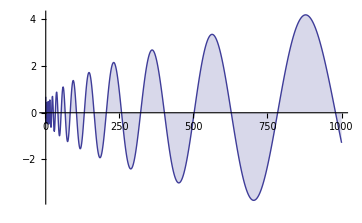

```mathematica
DiscretePlot[P5[j,14.134725141734695 ],{j,2,1000}]
```

```mathematica
N[Pi^2/6]
```

1.64493

```mathematica
N[ZetaZero[2]]
```

0.5+21.022 ⅈ

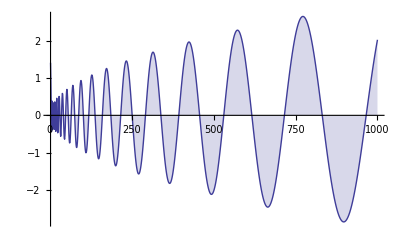

```mathematica
DiscretePlot[P5[j,21.022039638771556  ],{j,2,1000}]
```

```mathematica
N[ZetaZero[20]]
```

0.5+77.1448 ⅈ

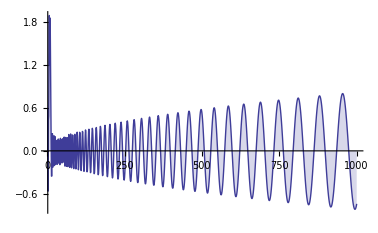

```mathematica
DiscretePlot[P5[j,77.1448400688748   ],{j,2,1000}]
```

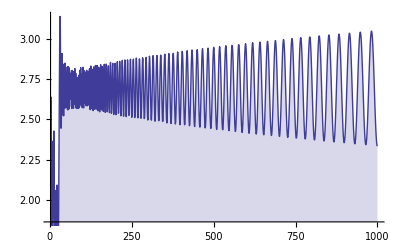

```mathematica
DiscretePlot[P5[j,177.1448400688748   ],{j,2,1000}]
```

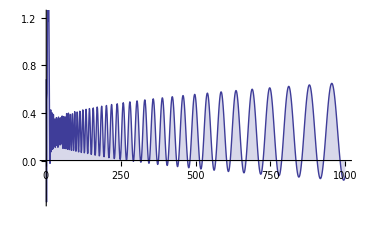

```mathematica
DiscretePlot[P6[j,.6, 77.1448400688748   ],{j,2,1000}]
```

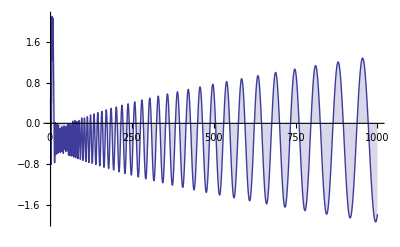

```mathematica
DiscretePlot[P6[j,.4, 77.1448400688748   ],{j,2,1000}]
```

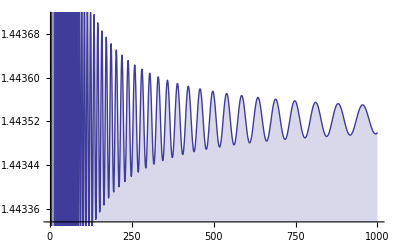

```mathematica
DiscretePlot[P6[j,2, 77.1448400688748   ],{j,2,1000}]
```

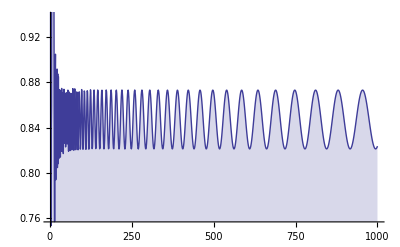

```mathematica
DiscretePlot[P6[j,1, 77.1448400688748   ],{j,2,1000}]
```

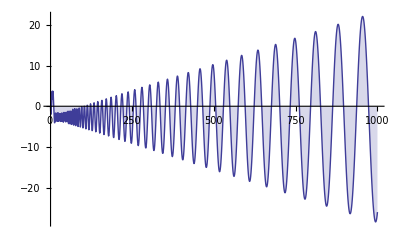

```mathematica
DiscretePlot[P6[j,0, 77.1448400688748   ],{j,2,1000}]
```

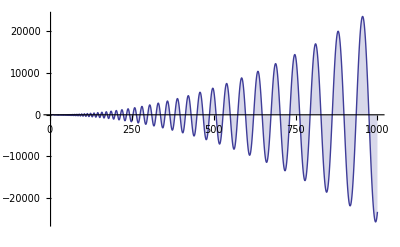

```mathematica
DiscretePlot[P6[j,-1, 77.1448400688748   ],{j,2,1000}]
```

```mathematica
N[ZetaZero[2000]]
```

0.5+2515.29 ⅈ

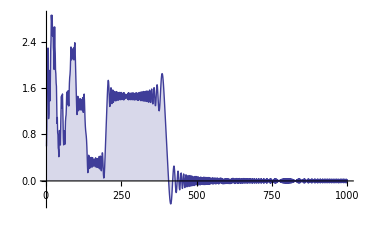

```mathematica
DiscretePlot[P5[j,2515.286482924713   ],{j,2,1000}]
```

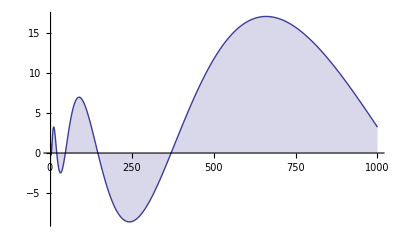

```mathematica
DiscretePlot[P6[j,.5, 3.1448400688748   ],{j,2,1000}]
```